```mathematica
Table[(D[1/Sqrt[x],{x,n}])/.x->1,{n,1,10}]
```

{-1/2,3/4,-15/8,105/16,-945/32,10395/64,-135135/128,2027025/256,-34459425/512,654729075/1024}

```mathematica
D[x^3,x]//Simplify
```

3 x^2

```mathematica
Fold[Plus,Map[(x-1)^n*#&,Table[(D[1/Sqrt[x],{x,n}])/.x->1,{n,1,10}]]]
```

(592978381 (-1+x)^n)/1024

```mathematica
-592978381/1024+10 x
```

-592978381/1024+10 x

```mathematica
Table[1/(Sqrt[x])//N,{x,1,10}]
```

{1.,0.707107,0.57735,0.5,0.447214,0.408248,0.377964,0.353553,0.333333,0.316228}

```mathematica
Table[(1-x)/2+(592978893 (-1+x))/1024//N,{x,1,10}]
```

{0.,579080.,1.15816×10^6,1.73724×10^6,2.31632×10^6,2.8954×10^6,3.47448×10^6,4.05356×10^6,4.63264×10^6,5.21172×10^6}

```mathematica
f[x_]:=1+Total[Table[((x-1)^n/Factorial[n])*((D[1/Sqrt[x],{x,n}])/.x->1),{n,1,20}]]
```

```mathematica
D[1/Sqrt[x],{x,n}]/.n->1
```

-1/(2 x^(3/2))

```mathematica
-1/(2 x^(3/2))/.(x->1)
```

-1/2

```mathematica
1+Total[Table[((x-1)^n/Factorial[n])*((D[1/Sqrt[x],{x,n}])/.x->1),{n,1,1}]]
```

1+(1-x)/2

```mathematica
Total[Map[#[[1]]*#[[3]]/#[[2]]&,Table[{(x-1)^n,Factorial[n],((D[1/Sqrt[x],{x,n}])/.x->1)},{n,1,4}]]]
```

(1-x)/2+3/8 (-1+x)^2-5/16 (-1+x)^3+35/128 (-1+x)^4

```mathematica
f[x_]:=1+(1-x)/2+3/8 (-1+x)^2-5/16 (-1+x)^3+35/128 (-1+x)^4
```

```mathematica
Taylor[f_,a_,n_]:=Sum[(D[f,{x,t}]/.x->a)*(x-a)^t/Factorial[t],{t,0,n}]
```

```mathematica
Taylor[1/Sqrt[x],1,10]
```

1+(1-x)/2+3/8 (-1+x)^2-5/16 (-1+x)^3+35/128 (-1+x)^4-63/256 (-1+x)^5+(231 (-1+x)^6)/1024-(429 (-1+x)^7)/2048+(6435 (-1+x)^8)/32768-(12155 (-1+x)^9)/65536+(46189 (-1+x)^10)/262144

```mathematica
Table[1+(1-x)/2+3/8 (-1+x)^2-5/16 (-1+x)^3+35/128 (-1+x)^4-63/256 (-1+x)^5+(231 (-1+x)^6)/1024-(429 (-1+x)^7)/2048+(6435 (-1+x)^8)/32768-(12155 (-1+x)^9)/65536+(46189 (-1+x)^10)/262144//N,{x,0,1,0.1}]
```

{3.70014,2.74418,2.17247,1.81552,1.5797,1.41406,1.29098,1.19523,1.11803,1.05409,1.}

```mathematica
Table[1/(Sqrt[x])//N,{x,0,1,0.1}]
```

Power::infy: Infinite expression 1/0. encountered.

{ComplexInfinity,3.16228,2.23607,1.82574,1.58114,1.41421,1.29099,1.19523,1.11803,1.05409,1.}

```mathematica
Taylor[1/Sqrt[x],1,100]
```

1+(1-x)/2+3/8 (-1+x)^2-5/16 (-1+x)^3+35/128 (-1+x)^4-63/256 (-1+x)^5+(231 (-1+x)^6)/1024-(429 (-1+x)^7)/2048+(6435 (-1+x)^8)/32768-(12155 (-1+x)^9)/65536+(46189 (-1+x)^10)/262144-(88179 (-1+x)^11)/524288+(676039 (-1+x)^12)/4194304-(1300075 (-1+x)^13)/8388608+(5014575 (-1+x)^14)/33554432-(9694845 (-1+x)^15)/67108864+(300540195 (-1+x)^16)/2147483648-(583401555 (-1+x)^17)/4294967296+(2268783825 (-1+x)^18)/17179869184-(4418157975 (-1+x)^19)/34359738368+(34461632205 (-1+x)^20)/274877906944-(67282234305 (-1+x)^21)/549755813888+(263012370465 (-1+x)^22)/2199023255552-(514589420475 (-1+x)^23)/4398046511104+(8061900920775 (-1+x)^24)/70368744177664-(15801325804719 (-1+x)^25)/140737488355328+(61989816618513 (-1+x)^26)/562949953421312-(121683714103007 (-1+x)^27)/1125899906842624+(956086325095055 (-1+x)^28)/9007199254740992-(1879204156221315 (-1+x)^29)/18014398509481984+(7391536347803839 (-1+x)^30)/72057594037927936-(14544636039226909 (-1+x)^31)/144115188075855872+(916312070471295267 (-1+x)^32)/9223372036854775808-(1804857108504066435 (-1+x)^33)/18446744073709551616+(7113260368810144185 (-1+x)^34)/73786976294838206464-(14023284727082855679 (-1+x)^35)/147573952589676412928+(110628135069209194801 (-1+x)^36)/1180591620717411303424-(218266320541953276229 (-1+x)^37)/2361183241434822606848+(861577581086657669325 (-1+x)^38)/9444732965739290427392-(1701063429324939500975 (-1+x)^39)/18889465931478580854784+(26876802183334044115405 (-1+x)^40)/302231454903657293676544-(53098072606098965203605 (-1+x)^41)/604462909807314587353088+(209863810776486386280915 (-1+x)^42)/2417851639229258349412352-(414847067813984717066925 (-1+x)^43)/4835703278458516698824704+(3281063172710606398620225 (-1+x)^44)/38685626227668133590597632-(6489213830472088210604445 (-1+x)^45)/77371252455336267181195264+(25674715590128696833261065 (-1+x)^46)/309485009821345068724781056-(50803160635786570329644235 (-1+x)^47)/618970019642690137449562112+(1608766753466574727105400775 (-1+x)^48)/19807040628566084398385987584-(3184701532372607112841303575 (-1+x)^49)/39614081257132168796771975168+(12611418068195524166851562157 (-1+x)^50)/158456325028528675187087900672-(24975553429171528252000152507 (-1+x)^51)/316912650057057350374175801344+(197883231015743646919693516017 (-1+x)^52)/2535301200456458802993406410752-(392032816163265715595619229845 (-1+x)^53)/5070602400912917605986812821504+(1553611530721090058101157688645 (-1+x)^54)/20282409603651670423947251286016-(3078975579065433024236839782951 (-1+x)^55)/40564819207303340847894502572032+(48823755610894723670041316558223 (-1+x)^56)/649037107316853453566312041152512-(96790954105808838152888925808407 (-1+x)^57)/1298074214633706907132624082305024+(383826197316138496123525050619545 (-1+x)^58)/5192296858534827628530496329220096-(761146865864206848244956456313335 (-1+x)^59)/10384593717069655257060992658440192+(6038431802522707662743321220085791 (-1+x)^60)/83076749736557242056487941267521536-(11977872919758157822818719141481651 (-1+x)^61)/166153499473114484112975882535043072+(47525108681621077813119434012975583 (-1+x)^62)/664613997892457936451903530140172288-(94295850558771979787935384946380125 (-1+x)^63)/1329227995784915872903807060280344576+(11975573020964041433067793888190275875 (-1+x)^64)/170141183460469231731687303715884105728-(23766906456990174536396083255023778275 (-1+x)^65)/340282366920938463463374607431768211456+(94347416541385238311148088072973180425 (-1+x)^66)/1361129467683753853853498429727072845824-(187286662686630398438547697219484074575 (-1+x)^67)/2722258935367507707706996859454145691648+(1487276438982064928776702301448844121625 (-1+x)^68)/21778071482940061661655974875633165533184-(2952998146964389786121858192731762966125 (-1+x)^69)/43556142965880123323311949751266331066368+(11727621212230005150598236822563287208325 (-1+x)^70)/174224571863520493293247799005065324265472-(23290064660907475017385230872977795723575 (-1+x)^71)/348449143727040986586495598010130648530944+(370053249612196547498454223870647198719025 (-1+x)^72)/5575186299632655785383929568162090376495104-(735037276626965745031176198099230737181625 (-1+x)^73)/11150372599265311570767859136324180752990208+(2920283234166593635664402732988835631505375 (-1+x)^74)/44601490397061246283071436545296723011960832-(5801629358544299356186613429537820121257345 (-1+x)^75)/89202980794122492566142873090593446023921664+(46107685954746800146535717255800570437361005 (-1+x)^76)/713623846352979940529142984724747568191373312-(91616570793198187304155386235551782817093945 (-1+x)^77)/1427247692705959881058285969449495136382746624+(364117140331941513644720124782321188119219525 (-1+x)^78)/5708990770823839524233143877797980545530986496-(723625202938162248635709615073726918160980575 (-1+x)^79)/11417981541647679048466287755595961091061972992+(23011281453433559506615565759344515997519182285 (-1+x)^80)/365375409332725729550921208179070754913983135744-(45738473012380284945248223299437865130871461085 (-1+x)^81)/730750818665451459101842416358141509827966271488+(181838319537024059660377082873374927227610930655 (-1+x)^82)/2923003274661805836407369665432566039311865085952-(361485815947096022216412273182010397500672332025 (-1+x)^83)/5846006549323611672814739330865132078623730171904+(2874672917293573129054326172447416018219632354675 (-1+x)^84)/46768052394588893382517914646921056628989841375232-(5715526153207221868355072036983685965636680799295 (-1+x)^85)/93536104789177786765035829293842113257979682750464+(22729185399963603243923658565679309305206335271615 (-1+x)^86)/374144419156711147060143317175368453031918731001856-(45197115795329923691940148642097936894260873586085 (-1+x)^87)/748288838313422294120286634350736906063837462003712+(719045024016612422371775092033376268772332079778625 (-1+x)^88)/11972621413014756705924586149611790497021399392059392-(1430010890460004480447238104380984264861828967649625 (-1+x)^89)/23945242826029513411849172299223580994042798784118784+(5688265542052017822223458237426581853561497449095175 (-1+x)^90)/95780971304118053647396689196894323976171195136475136-(11314022671554013470576329021694629840600341080068425 (-1+x)^91)/191561942608236107294793378393788647952342390272950272+(90020267343234107178933400476961620036080974680544425 (-1+x)^92)/1532495540865888858358347027150309183618739122183602176-(179072574822562471269921280518687093620161078665599125 (-1+x)^93)/3064991081731777716716694054300618367237478244367204352+(712480244506791109095218711850946521424896206605681625 (-1+x)^94)/12259964326927110866866776217202473468949912977468817408-(1417460696966142311778908805682409395255846137352356075 (-1+x)^95)/24519928653854221733733552434404946937899825954937634816+(90244997706844393849923860628446731497955537411433336775 (-1+x)^96)/1569275433846670190958947355801916604025588861116008628224-(179559634612587299103456753621548651330983698148521999975 (-1+x)^97)/3138550867693340381917894711603833208051177722232017256448+(714574056111316802554572795024530347133506553856363061125 (-1+x)^98)/12554203470773361527671578846415332832204710888928069025792-(1421930192463933435386372127473055337225260516259631545875 (-1+x)^99)/25108406941546723055343157692830665664409421777856138051584+(11318564332012910145675522134685520484313073709426667105165 (-1+x)^100)/200867255532373784442745261542645325315275374222849104412672

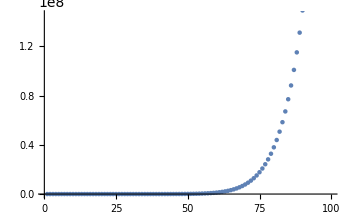

```mathematica
Table[(1+(1-x)/2+3/8 (-1+x)^2-5/16 (-1+x)^3+35/128 (-1+x)^4-63/256 (-1+x)^5+(231 (-1+x)^6)/1024-(429 (-1+x)^7)/2048+(6435 (-1+x)^8)/32768-(12155 (-1+x)^9)/65536+(46189 (-1+x)^10)/262144)-(1/(Sqrt[x]))//N,{x,0.01,10,0.1}]//ListPlot
```

```mathematica
Table[(1+(1-x)/2+3/8 (-1+x)^2-5/16 (-1+x)^3+35/128 (-1+x)^4-63/256 (-1+x)^5+(231 (-1+x)^6)/1024-(429 (-1+x)^7)/2048+(6435 (-1+x)^8)/32768-(12155 (-1+x)^9)/65536+(46189 (-1+x)^10)/262144-(88179 (-1+x)^11)/524288+(676039 (-1+x)^12)/4194304-(1300075 (-1+x)^13)/8388608+(5014575 (-1+x)^14)/33554432-(9694845 (-1+x)^15)/67108864+(300540195 (-1+x)^16)/2147483648-(583401555 (-1+x)^17)/4294967296+(2268783825 (-1+x)^18)/17179869184-(4418157975 (-1+x)^19)/34359738368+(34461632205 (-1+x)^20)/274877906944-(67282234305 (-1+x)^21)/549755813888+(263012370465 (-1+x)^22)/2199023255552-(514589420475 (-1+x)^23)/4398046511104+(8061900920775 (-1+x)^24)/70368744177664-(15801325804719 (-1+x)^25)/140737488355328+(61989816618513 (-1+x)^26)/562949953421312-(121683714103007 (-1+x)^27)/1125899906842624+(956086325095055 (-1+x)^28)/9007199254740992-(1879204156221315 (-1+x)^29)/18014398509481984+(7391536347803839 (-1+x)^30)/72057594037927936-(14544636039226909 (-1+x)^31)/144115188075855872+(916312070471295267 (-1+x)^32)/9223372036854775808-(1804857108504066435 (-1+x)^33)/18446744073709551616+(7113260368810144185 (-1+x)^34)/73786976294838206464-(14023284727082855679 (-1+x)^35)/147573952589676412928+(110628135069209194801 (-1+x)^36)/1180591620717411303424-(218266320541953276229 (-1+x)^37)/2361183241434822606848+(861577581086657669325 (-1+x)^38)/9444732965739290427392-(1701063429324939500975 (-1+x)^39)/18889465931478580854784+(26876802183334044115405 (-1+x)^40)/302231454903657293676544-(53098072606098965203605 (-1+x)^41)/604462909807314587353088+(209863810776486386280915 (-1+x)^42)/2417851639229258349412352-(414847067813984717066925 (-1+x)^43)/4835703278458516698824704+(3281063172710606398620225 (-1+x)^44)/38685626227668133590597632-(6489213830472088210604445 (-1+x)^45)/77371252455336267181195264+(25674715590128696833261065 (-1+x)^46)/309485009821345068724781056-(50803160635786570329644235 (-1+x)^47)/618970019642690137449562112+(1608766753466574727105400775 (-1+x)^48)/19807040628566084398385987584-(3184701532372607112841303575 (-1+x)^49)/39614081257132168796771975168+(12611418068195524166851562157 (-1+x)^50)/158456325028528675187087900672-(24975553429171528252000152507 (-1+x)^51)/316912650057057350374175801344+(197883231015743646919693516017 (-1+x)^52)/2535301200456458802993406410752-(392032816163265715595619229845 (-1+x)^53)/5070602400912917605986812821504+(1553611530721090058101157688645 (-1+x)^54)/20282409603651670423947251286016-(3078975579065433024236839782951 (-1+x)^55)/40564819207303340847894502572032+(48823755610894723670041316558223 (-1+x)^56)/649037107316853453566312041152512-(96790954105808838152888925808407 (-1+x)^57)/1298074214633706907132624082305024+(383826197316138496123525050619545 (-1+x)^58)/5192296858534827628530496329220096-(761146865864206848244956456313335 (-1+x)^59)/10384593717069655257060992658440192+(6038431802522707662743321220085791 (-1+x)^60)/83076749736557242056487941267521536-(11977872919758157822818719141481651 (-1+x)^61)/166153499473114484112975882535043072+(47525108681621077813119434012975583 (-1+x)^62)/664613997892457936451903530140172288-(94295850558771979787935384946380125 (-1+x)^63)/1329227995784915872903807060280344576+(11975573020964041433067793888190275875 (-1+x)^64)/170141183460469231731687303715884105728-(23766906456990174536396083255023778275 (-1+x)^65)/340282366920938463463374607431768211456+(94347416541385238311148088072973180425 (-1+x)^66)/1361129467683753853853498429727072845824-(187286662686630398438547697219484074575 (-1+x)^67)/2722258935367507707706996859454145691648+(1487276438982064928776702301448844121625 (-1+x)^68)/21778071482940061661655974875633165533184-(2952998146964389786121858192731762966125 (-1+x)^69)/43556142965880123323311949751266331066368+(11727621212230005150598236822563287208325 (-1+x)^70)/174224571863520493293247799005065324265472-(23290064660907475017385230872977795723575 (-1+x)^71)/348449143727040986586495598010130648530944+(370053249612196547498454223870647198719025 (-1+x)^72)/5575186299632655785383929568162090376495104-(735037276626965745031176198099230737181625 (-1+x)^73)/11150372599265311570767859136324180752990208+(2920283234166593635664402732988835631505375 (-1+x)^74)/44601490397061246283071436545296723011960832-(5801629358544299356186613429537820121257345 (-1+x)^75)/89202980794122492566142873090593446023921664+(46107685954746800146535717255800570437361005 (-1+x)^76)/713623846352979940529142984724747568191373312-(91616570793198187304155386235551782817093945 (-1+x)^77)/1427247692705959881058285969449495136382746624+(364117140331941513644720124782321188119219525 (-1+x)^78)/5708990770823839524233143877797980545530986496-(723625202938162248635709615073726918160980575 (-1+x)^79)/11417981541647679048466287755595961091061972992+(23011281453433559506615565759344515997519182285 (-1+x)^80)/365375409332725729550921208179070754913983135744-(45738473012380284945248223299437865130871461085 (-1+x)^81)/730750818665451459101842416358141509827966271488+(181838319537024059660377082873374927227610930655 (-1+x)^82)/2923003274661805836407369665432566039311865085952-(361485815947096022216412273182010397500672332025 (-1+x)^83)/5846006549323611672814739330865132078623730171904+(2874672917293573129054326172447416018219632354675 (-1+x)^84)/46768052394588893382517914646921056628989841375232-(5715526153207221868355072036983685965636680799295 (-1+x)^85)/93536104789177786765035829293842113257979682750464+(22729185399963603243923658565679309305206335271615 (-1+x)^86)/374144419156711147060143317175368453031918731001856-(45197115795329923691940148642097936894260873586085 (-1+x)^87)/748288838313422294120286634350736906063837462003712+(719045024016612422371775092033376268772332079778625 (-1+x)^88)/11972621413014756705924586149611790497021399392059392-(1430010890460004480447238104380984264861828967649625 (-1+x)^89)/23945242826029513411849172299223580994042798784118784+(5688265542052017822223458237426581853561497449095175 (-1+x)^90)/95780971304118053647396689196894323976171195136475136-(11314022671554013470576329021694629840600341080068425 (-1+x)^91)/191561942608236107294793378393788647952342390272950272+(90020267343234107178933400476961620036080974680544425 (-1+x)^92)/1532495540865888858358347027150309183618739122183602176-(179072574822562471269921280518687093620161078665599125 (-1+x)^93)/3064991081731777716716694054300618367237478244367204352+(712480244506791109095218711850946521424896206605681625 (-1+x)^94)/12259964326927110866866776217202473468949912977468817408-(1417460696966142311778908805682409395255846137352356075 (-1+x)^95)/24519928653854221733733552434404946937899825954937634816+(90244997706844393849923860628446731497955537411433336775 (-1+x)^96)/1569275433846670190958947355801916604025588861116008628224-(179559634612587299103456753621548651330983698148521999975 (-1+x)^97)/3138550867693340381917894711603833208051177722232017256448+(714574056111316802554572795024530347133506553856363061125 (-1+x)^98)/12554203470773361527671578846415332832204710888928069025792-(1421930192463933435386372127473055337225260516259631545875 (-1+x)^99)/25108406941546723055343157692830665664409421777856138051584+(11318564332012910145675522134685520484313073709426667105165 (-1+x)^100)/200867255532373784442745261542645325315275374222849104412672)-(1/(Sqrt[x]))//N,{x,0.01,7,0.1}]//ListPlot
```

-Graphics-

```mathematica
Taylor[Cos[x],0,100]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000-x^18/6402373705728000+x^20/2432902008176640000-x^22/1124000727777607680000+x^24/620448401733239439360000-x^26/403291461126605635584000000+x^28/304888344611713860501504000000-x^30/265252859812191058636308480000000+x^32/263130836933693530167218012160000000-x^34/295232799039604140847618609643520000000+x^36/371993326789901217467999448150835200000000-x^38/523022617466601111760007224100074291200000000+x^40/815915283247897734345611269596115894272000000000-x^42/1405006117752879898543142606244511569936384000000000+x^44/2658271574788448768043625811014615890319638528000000000-x^46/5502622159812088949850305428800254892961651752960000000000+x^48/12413915592536072670862289047373375038521486354677760000000000-x^50/30414093201713378043612608166064768844377641568960512000000000000+x^52/80658175170943878571660636856403766975289505440883277824000000000000-x^54/230843697339241380472092742683027581083278564571807941132288000000000000+x^56/710998587804863451854045647463724949736497978881168458687447040000000000000-x^58/2350561331282878571829474910515074683828862318181142924420699914240000000000000+x^60/8320987112741390144276341183223364380754172606361245952449277696409600000000000000-x^62/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000+x^64/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000-x^66/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000+x^68/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000-x^70/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000+x^72/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000-x^74/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000+x^76/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000-x^78/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000+x^80/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000-x^82/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000+x^84/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000-x^86/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000+x^88/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000-x^90/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000+x^92/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000-x^94/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000+x^96/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000-x^98/9426890448883247745626185743057242473809693764078951663494238777294707070023223798882976159207729119823605850588608460429412647567360000000000000000000000+x^100/93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000